```mathematica
"1 2 3 4"/." "->"---"
```

1 2 3 4

```mathematica
StringCases["+string +patterns are +quite +easy","+"~~_]
```

{+s,+p,+q,+e}

```mathematica
StringTemplate["1 2 3 4"][<|" "->"---"|>]
```

1 2 3 4

```mathematica
StringReplace["1 2 3 4", " "->"---"]
```

1---2---3---4

```mathematica
Select[StringCases[WikipediaData["computers"],DigitCharacter..],StringLength[#]==4&]//Sort
```

{1000,1235,1357,1357,1595,1613,1620,1630,1640,1770,1831,1833,1835,1872,1872,1876,1876,1888,1897,1901,1906,1920,1925,1927,1930,1934,1936,1936,1937,1938,1939,1940,1941,1942,1943,1943,1943,1943,1944,1945,1945,1945,1945,1945,1945,1947,1947,1947,1948,1948,1950,1950,1950,1950,1950,1951,1951,1952,1953,1953,1955,1955,1955,1957,1958,1958,1959,1959,1959,1959,1960,1961,1962,1964,1967,1968,1970,1970,1970,1970,1990,2000,2000,2000,2000,2016,2400,2468,4000,4004,5000,5100,6502,6510}

```mathematica
StringCases[WikipediaData["computers"],"==="~~Shortest[x__]~~"==="->x]
```

{ Pre-20th century , First computing device , Analog computers , Digital computers ,= Electromechanical ,= Vacuum tubes and digital electronic circuits , Modern computers ,= Concept of modern computer ,= Stored programs ,= Transistors ,= Integrated circuits , Mobile computers , By architecture , By size, form-factor and purpose , History of computing hardware , Other hardware topics , Input devices , Output devices , Control unit , Central processing unit (CPU) , Arithmetic logic unit (ALU) , Memory , Input/output (I/O) , Multitasking , Multiprocessing , Languages , Programs ,= Stored program architecture ,= Machine code ,= Programming language ,== Low-level languages ,== High-level languages ,= Program design ,= Bugs , Computer architecture paradigms , Artificial intelligence }

```mathematica
StringRiffle[StringSplit["1 2 3 4", " "], "---"]
```

1---2---3---4

```mathematica
Table[StringTemplate["``+``=``"][i, j, i+j],{i,9},{j,9}]//Grid
```

1+1=2 | 1+2=3 | 1+3=4 | 1+4=5 | 1+5=6 | 1+6=7 | 1+7=8 | 1+8=9 | 1+9=10
2+1=3 | 2+2=4 | 2+3=5 | 2+4=6 | 2+5=7 | 2+6=8 | 2+7=9 | 2+8=10 | 2+9=11
3+1=4 | 3+2=5 | 3+3=6 | 3+4=7 | 3+5=8 | 3+6=9 | 3+7=10 | 3+8=11 | 3+9=12
4+1=5 | 4+2=6 | 4+3=7 | 4+4=8 | 4+5=9 | 4+6=10 | 4+7=11 | 4+8=12 | 4+9=13
5+1=6 | 5+2=7 | 5+3=8 | 5+4=9 | 5+5=10 | 5+6=11 | 5+7=12 | 5+8=13 | 5+9=14
6+1=7 | 6+2=8 | 6+3=9 | 6+4=10 | 6+5=11 | 6+6=12 | 6+7=13 | 6+8=14 | 6+9=15
7+1=8 | 7+2=9 | 7+3=10 | 7+4=11 | 7+5=12 | 7+6=13 | 7+7=14 | 7+8=15 | 7+9=16
8+1=9 | 8+2=10 | 8+3=11 | 8+4=12 | 8+5=13 | 8+6=14 | 8+7=15 | 8+8=16 | 8+9=17
9+1=10 | 9+2=11 | 9+3=12 | 9+4=13 | 9+5=14 | 9+6=15 | 9+7=16 | 9+8=17 | 9+9=18

```mathematica
Select[IntegerName[Range[50]],StringMatchQ[#,___~~"i"~~___~~"e"~~___]&]
```

{five,nine,thirteen,fifteen,sixteen,eighteen,nineteen,twenty-five,twenty-nine,thirty-one,thirty-three,thirty-five,thirty-seven,thirty-eight,thirty-nine,forty-five,forty-nine}

```mathematica
IntegerName[Range[50]]
```

{one,two,three,four,five,six,seven,eight,nine,ten,eleven,twelve,thirteen,fourteen,fifteen,sixteen,seventeen,eighteen,nineteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty}

```mathematica
ToUpperCase[Select[TextWords[WikipediaData["computers"]],StringLength[#]==2&]]
```

{IS,BE,TO,OF,OR,TO,OF,TO,AN,OF,BE,TO,AS,AS,BE,OF,IN,OR,AS,OF,AS,AS,IS,ON,IT,OF,OF,AS,IN,IN,TO,AS,IN,II,IN,BY,IC,IN,TO,IN,OF,AT,AS,BY,TO,TO,OF,AT,IN,OF,OF,OF,IN,TO,TO,BE,AN,OF,TO,BE,TO,OF,IN,IN,BY,OF,HE,OF,TO,OR,OF,OF,AS,BE,BY,OF,IN,IS,AN,V.,OF,TO,OF,IS,OF,TO,IN,AS,TO,OF,OF,OF,OR,IN,OF,IS,IN,AS,AS,BC,OF,OR,IN,BE,ON,ON,IT,TO,AS,AN,TO,OF,IS,TO,BE,TO,J.,DE,IT,TO,IT,IN,IN,OF,TO,C.,BC,OF,OF,TO,OF,TO,BY,IN,IN,IN,OR,BC,IS,TO,OF,AN,OF,OF,IN,AN,BY,OF,IN,AN,C.,AD,IN,AS,IN,IN,TO,OF,BY,IT,OF,OF,IT,IS,AS,AS,AS,AS,OF,AS,ON,IN,BY,OF,BE,IN,IT,BE,TO,IS,AT,ET,OF,OF,AD,IS,BC,TO,AD,OF,BY,IN,OF,TO,IN,IT,OF,TO,AT,TO,BY,TO,IN,OF,HE,BY,OF,IN,OF,OF,OR,TO,IN,AN,OF,OF,HE,IN,ON,TO,IN,IN,HE,AN,OF,TO,BE,TO,AT,TO,AS,BE,TO,TO,BE,IN,AN,IN,OF,IT,BE,IN,AS,OF,TO,BE,BY,OF,OF,TO,TO,BE,TO,AS,AS,TO,AN,TO,OF,IN,HE,OF,IN,IN,OF,BY,OR,OF,AS,OF,BY,IN,TO,BY,IN,BY,OF,OF,BY,H.,L.,AT,IN,ON,OF,BY,H.,W.,OF,BY,OF,IN,IN,AS,BY,AN,TO,TO,OF,AT,II,IN,AS,TO,BY,Z2,BY,IN,OF,OF,AN,UP,Z3,Z3,22,AT,OF,10,HZ,ON,BE,IN,64,OF,OR,IT,TO,IN,AS,IN,TO,AT,Z3,BE,TO,BE,AT,AT,IN,IN,TO,OF,HE,IN,OF,AN,OF,IN,US,E.,OF,IN,IN,II,AT,OF,AT,OF,BY,TO,SZ,TO,HE,IN,TO,IT,ON,18,ON,IT,OF,IT,OF,TO,OF,ON,IT,MK,II,MK,TO,MK,II,IN,II,TO,IN,TO,IT,IT,ON,BY,OF,IT,TO,BE,OF,OF,AS,IT,OF,TO,BE,IT,OR,IT,TO,TO,20,80,OF,J.,AT,OF,TO,AT,OF,30,OF,OF,OF,OF,OF,BY,IN,ON,HE,IS,AS,HE,IS,OF,IS,BY,ON,TO,BE,OF,IS,IN,OF,TO,TO,OF,IN,OF,BY,TO,BE,IS,TO,TO,OF,OF,BY,AN,IN,OF,BY,IN,IN,ON,AN,AT,OF,OF,ON,IN,IT,AT,OF,BY,C.,ON,21,IT,AS,BY,OF,IT,TO,OF,TO,AS,AS,OF,AT,TO,IT,TO,IN,BY,IT,TO,OF,IN,AT,OF,OF,TO,IN,IN,OF,J.,TO,AN,IN,OF,IN,OF,BY,IN,AT,IN,BY,IN,IN,TO,OF,TO,SO,OF,OF,IN,TO,ON,TO,OF,OF,OF,OF,IN,BY,IN,OF,TO,IN,TO,ON,SO,IT,TO,OF,BY,OF,AT,AS,BY,M.,AT,IN,IT,BE,OF,IT,TO,IN,TO,IT,OF,AS,TO,OF,IN,TO,IS,IN,IS,OF,IN,OF,IC,OF,BY,OF,OF,OF,AN,AT,ON,IN,IN,ON,BY,AT,AT,IN,ON,12,IN,OF,AS,OF,OF,IC,IC,IC,IT,TO,UP,OF,AN,IC,AT,IT,OF,OF,IC,BY,IN,IN,ON,BY,AT,IN,BY,AT,IN,OF,IN,BY,IN,OF,IT,IC,TO,BE,BY,AT,IN,IC,IN,BY,OF,BY,AT,IN,IC,BY,AT,IN,IN,OF,TO,OF,AN,IN,OF,OF,IS,TO,OF,ON,OF,IT,IS,BY,IC,AT,IN,IC,OF,ON,ON,ON,OR,OF,OR,IF,IS,AS,ON,OR,ON,OF,IS,TO,TO,AS,TO,IN,AS,OF,OF,OF,OF,OF,AN,AS,TO,BE,IN,AS,BY,OF,IN,IN,IN,TO,BY,ON,OF,ON,BY,ON,ON,OF,BE,IN,OF,BY,BY,NO,NO,PC,PC,PC,PC,PC,PC,PC,PC,ON,IN,AS,AN,OR,AP,IF,IT,AS,OF,OF,OF,BY,OF,OF,OF,TO,OF,BE,OR,ON,BY,OF,AN,OF,SO,IS,ON,IT,IT,IN,IN,SO,OR,OF,OF,OR,OF,IS,TO,OF,IS,TO,BE,OR,OF,IS,BY,OF,AS,OF,PC,OR,IT,OF,IN,OF,OF,TO,TO,IS,OF,IN,IS,TO,BE,IS,AS,IS,OF,BE,OR,IN,ON,OF,BY,OF,OR,OF,SO,IT,TO,IN,OR,AN,OF,IS,TO,AN,OR,IF,AN,OR,TO,TO,TO,OR,TO,OR,AN,TO,IS,OF,IT,BE,BY,IN,TO,TO,BE,AS,BY,OF,OF,TO,AN,IS,IN,IN,IS,OF,TO,AS,OF,ON,IS,OF,OF,OF,BE,TO,OR,AS,ON,TO,IS,OF,BE,TO,IT,BE,TO,IT,TO,DO,SO,IF,AN,OR,ON,IS,TO,OR,IS,64,65,OR,BE,TO,ON,BE,AS,OF,BE,OR,BE,TO,OR,TO,IS,IN,TO,IS,IN,IN,BE,OF,IT,IS,TO,TO,AS,OF,IN,IS,UP,TO,IN,OF,IS,TO,28,TO,OR,TO,TO,BE,OR,IN,OF,OR,OF,IN,IF,IT,BE,OR,OF,OF,OF,BE,TO,ON,OF,TO,TO,IS,AS,IS,ON,TO,IS,TO,IN,OR,OR,BE,TO,IT,IS,IT,IS,TO,IN,OF,TO,IS,IN,PC,IS,ON,OR,IN,DO,OF,BE,IN,IN,IS,IT,IS,AS,IT,IS,IT,IS,SO,IS,TO,IS,BE,OR,OF,TO,ON,IS,BY,OR,TO,ON,AS,AS,IS,OF,IN,OR,TO,3D,IN,BE,AS,IN,IN,IT,IS,TO,OF,IS,BY,IN,BY,IS,IS,AN,TO,IT,DO,BY,IT,TO,TO,IF,AT,BE,OF,IT,AT,IS,IN,OF,IS,IS,OF,IN,OF,TO,TO,IS,TO,IN,TO,OF,IT,IS,OF,TO,IF,IS,TO,ON,OR,ON,IT,IT,IS,UP,TO,SO,BE,TO,IN,IN,AS,ON,IN,AS,IN,OF,TO,BE,TO,OF,TO,OF,AT,IN,AS,AS,TO,OF,DO,AS,IS,OF,OF,OR,IN,TO,IS,AS,OR,IT,IS,BE,ON,IS,IN,BE,AS,IN,AN,PC,IT,IS,OF,TO,BE,OF,IS,BE,IS,TO,OF,BE,TO,IT,ON,IN,OF,AN,IN,BE,OR,TO,OF,AS,DO,OF,OF,OF,OF,TO,TO,OF,TO,IN,TO,TO,TO,IN,TO,TO,OR,TO,IN,TO,ON,OR,BE,TO,SO,OF,BE,ON,OF,OR,BY,OF,IT,TO,TO,BE,TO,IN,AT,TO,AN,IN,OR,OF,GO,IN,OF,IS,IS,OF,IT,IS,TO,AS,TO,OF,TO,OF,OF,OF,ON,BE,TO,DO,IS,IN,TO,IT,PC,IN,OF,IN,AS,OR,TO,TO,SO,ON,TO,OF,OF,TO,IS,TO,IT,TO,OF,BE,AS,OF,BE,IN,AS,OF,IN,ON,IS,OF,OR,IN,OR,OF,IN,IS,IT,ON,IS,OF,IN,AS,IN,IT,IS,TO,AS,OF,IT,IS,TO,DO,SO,IN,BE,IS,OF,TO,AS,OR,AS,IN,IS,BY,AN,OF,TO,TO,NO,TO,BE,TO,BY,OR,AN,OR,AT,BY,AN,BY,OF,TO,OF,AN,AS,BE,IN,OR,OF,AN,BE,IN,PC,OF,IN,TO,IN,IN,IS,IS,IN,TO,OF,OR,TO,OF,TO,OF,TO,BE,BY,IT,IS,TO,TO,OF,OF,IS,OF,BY,BE,AS,OF,IS,OF,OF,OR,TO,AS,AS,AS,AS,OF,OF,OF,AN,OF,ON,IN,BE,OF,OR,IN,OR,TO,TO,AS,OR,TO,OR,TO,BE,BY,AN,AN,TO,OF,OF,OF,OR,AN,IN,AN,OF,IS,IN,IN,II,IN,TO,OF,TO,OF,AS,IN,AT,TO,BY,IN,AS,OF,OF,OF,TO,TO,OF,ON,AS,AS,OF,OF,AN,TO,IN,IN,OF,OF,IN,OF,IS,OF,TO,TO,IS,IN,TO,BE,OF,IS,OF,IS,OR,OR,OR,AS,IF,IS,IS,TO,OF,OF,AS,TO,BY,OF,BY,OF,TO,OF,OR,TO,OF,IS,OF,IS,IN,OF,OF,IS,TO,IN,IT,IS,TO,TO,OR,IN,OF,OF,TO,BY,TO,BE,TO,TO,OF,OF,AS,OF,AN,OF,TO,TO,BE,TO,OF,TO,AT,ON}

```mathematica
First@TextSentences[WikipediaData["computers"]]
```

A computer is a machine that can be instructed to carry out sequences of arithmetic or logical operations automatically via computer programming.

```mathematica
StringReplace[First@TextSentences[WikipediaData["computers"]],x:(Whitespace~~LetterCharacter~~LetterCharacter~~Whitespace):>ToUpperCase[x]]
```

A computer IS a machine that can BE instructed TO carry out sequences OF arithmetic OR logical operations automatically via computer programming.

```mathematica
StringTake[EntityClass["Country","Countries"],1]
```

StringTake::strse: String or list of strings expected at position 1 in StringTake[all countries, dependencies, and territories,1].

```mathematica
StringTake[EntityClass["Country","Countries"]["name"],1]
```

StringTake::strse: String or list of strings expected at position 1 in StringTake[{Missing[UnknownProperty,{Country,name}],Missing[UnknownProperty,{Country,name}],Missing[UnknownProperty,{Country,name}],Missing[UnknownProperty,{Country,name}],Missing[UnknownProperty,{Country,name}],«41»,Missing[UnknownProperty,{Country,name}],Missing[UnknownProperty,{Country,name}],Missing[UnknownProperty,{Country,name}],Missing[UnknownProperty,{Country,name}],«199»},1].

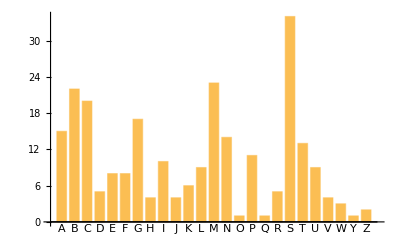

```mathematica
BarChart[Counts[StringTake[Last/@EntityList[EntityClass["Country","Countries"]],1]],ChartLabels->Automatic]
```

```mathematica
Grid[Table[StringJoin[TextString[i],"^",TextString[j],"=",TextString[i^j]],{i,5},{j,5}]]
```

1^1=1 | 1^2=1 | 1^3=1 | 1^4=1 | 1^5=1
2^1=2 | 2^2=4 | 2^3=8 | 2^4=16 | 2^5=32
3^1=3 | 3^2=9 | 3^3=27 | 3^4=81 | 3^5=243
4^1=4 | 4^2=16 | 4^3=64 | 4^4=256 | 4^5=1024
5^1=5 | 5^2=25 | 5^3=125 | 5^4=625 | 5^5=3125

```mathematica
$ImportFormats
```

{3DS,ACO,Affymetrix,AgilentMicroarray,AIFF,ApacheLog,ArcGRID,AU,AVI,Base64,BDF,Binary,Bit,BMP,BSON,Byte,BYU,BZIP2,CDED,CDF,Character16,Character32,Character8,CIF,Complex128,Complex256,Complex64,CSV,CUR,DAE,DBF,DICOM,DIF,DIMACS,Directory,DOT,DXF,EDF,EML,EPS,ExpressionJSON,ExpressionML,FASTA,FASTQ,FCS,FITS,FLAC,GenBank,GeoJSON,GeoTIFF,GIF,GPX,Graph6,Graphlet,GraphML,GRIB,GTOPO30,GXL,GZIP,HarwellBoeing,HDF,HDF5,HIN,HTML,HTTPRequest,HTTPResponse,ICC,ICNS,ICO,ICS,Ini,Integer128,Integer16,Integer24,Integer32,Integer64,Integer8,JavaProperties,JavaScriptExpression,JCAMP-DX,JPEG,JPEG2000,JSON,JSONLD,JVX,KML,LaTeX,LEDA,List,LWO,M4A,MAT,MathML,MBOX,MCTT,MDB,MESH,MGF,MIDI,MMCIF,MO,MOL,MOL2,MP3,MPS,MTP,MTX,MX,MXNet,NASACDF,NB,NDK,NetCDF,NEXUS,NOFF,NQuads,NTriples,OBJ,ODS,OFF,OGG,OpenEXR,Package,Pajek,PBM,PCAP,PCX,PDB,PDF,PGM,PHPIni,PLY,PNG,PNM,PPM,PXR,PythonExpression,QuickTime,Raw,RawBitmap,RawJSON,RDFXML,Real128,Real32,Real64,RIB,RLE,RSS,RTF,SCT,SDF,SDTS,SDTSDEM,SFF,SHP,SMA,SME,SMILES,SND,SP3,SPARQLQuery,SPARQLResultsJSON,SPARQLResultsXML,SPARQLUpdate,Sparse6,STL,String,SurferGrid,SXC,Table,TAR,TerminatedString,TeX,Text,TGA,TGF,TIFF,TIGER,TLE,TriG,TSV,Turtle,UBJSON,UnsignedInteger128,UnsignedInteger16,UnsignedInteger24,UnsignedInteger32,UnsignedInteger64,UnsignedInteger8,USGSDEM,UUE,VCF,VCS,VTK,WARC,WAV,Wave64,WDX,WebP,WLNet,WMLF,WXF,XBM,XHTML,XHTMLMathML,XLS,XLSX,XML,XPORT,XYZ,ZIP}

```mathematica
SocialMediaData["Facebook","FriendNetwork"]
```

CreateChannel::notauth: Unable to authenticate with Wolfram Cloud server. Please try authenticating again.

SocialMediaData[Facebook,FriendNetwork]

```mathematica
SocialMediaData["Twitter","Follow]
```

```mathematica
Dataset[{<|"x"->2,"y"->4,"z"->6|>,<|"x"->11,"y"->7,"z"->1|>}]
```

Dataset[<>]

```mathematica
ImageCollage[Graphics[Style[Disk[],#]]&/@(DominantColors[-Graphics-]//Union)]
```

-Graphics-

```mathematica
DominantColors[-Graphics-]//Union
```

{RGBColor[0.01104704610058328, 0.6334245472612682, 0.0846315835378611],RGBColor[0.020459968642587457, 0.45123780427862387, 0.05473052370133837],RGBColor[0.08388571878401521, 0.28221419531244146, 0.9307177178419573],RGBColor[0.18907626810794106, 0.41261269849313237, 0.9644271018841736],RGBColor[0.9124127002278871, 0.1555025298954583, 0.2003970701519166],RGBColor[0.9695867023268298, 0.6373093678620665, 0.030243851979709423],RGBColor[0.9999385697675148, 0.9999374338178256, 0.999937522496252]}

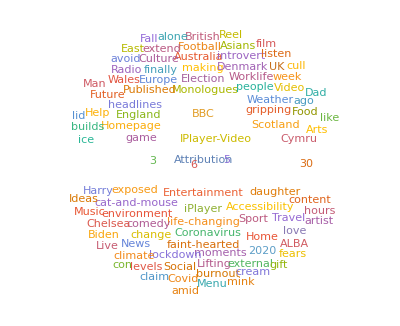

```mathematica
WordCloud[Import["http://bbc.co.uk"]]
```

```mathematica
Import["http://nps.gov","Images"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Select[Import["https://en.wikipedia.org/wiki/Ostrich","Images"],ImageInstanceQ[#,Entity["Species","Class:Aves"]]&]
```

{-Graphics-,-Graphics-,-Graphics-}

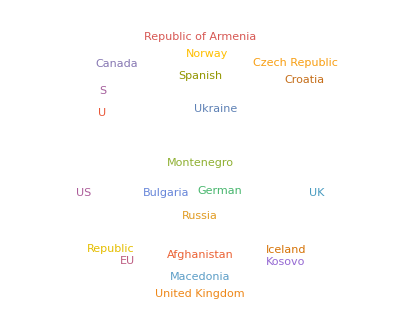

```mathematica
TextCases[Import["http://nato.int"],"Country"]//WordCloud
```

```mathematica
Import["https://en.wikipedia.org","Hyperlinks"]
```

{https://en.wikipedia.org/wiki/Wikipedia,https://en.wikipedia.org/wiki/Free_content,https://en.wikipedia.org/wiki/Encyclopedia,https://en.wikipedia.org/wiki/Help:Introduction_to_Wikipedia,https://en.wikipedia.org/wiki/Special:Statistics,https://en.wikipedia.org/wiki/English_language,https://en.wikipedia.org/wiki/Portal:The_arts,https://en.wikipedia.org/wiki/Portal:Biography,https://en.wikipedia.org/wiki/Portal:Geography,https://en.wikipedia.org/wiki/Portal:History,https://en.wikipedia.org/wiki/Portal:Mathematics,https://en.wikipedia.org/wiki/Portal:Science,https://en.wikipedia.org/wiki/Portal:Society,https://en.wikipedia.org/wiki/Portal:Technology,https://en.wikipedia.org/wiki/Wikipedia:Contents/Portals,https://en.wikipedia.org/wiki/File:Arms_of_Clifford.svg,https://en.wikipedia.org/wiki/Henry_Clifford,_10th_Baron_Clifford,https://en.wikipedia.org/wiki/Peerage_of_England,https://en.wikipedia.org/wiki/House_of_Lancaster,https://en.wikipedia.org/wiki/Henry_VII_of_England,https://en.wikipedia.org/wiki/Henry_Clifford,_1st_Earl_of_Cumberland,https://en.wikipedia.org/wiki/Henry_VIII,https://en.wikipedia.org/wiki/Battle_of_Flodden,https://en.wikipedia.org/wiki/Henry_Clifford,_10th_Baron_Clifford,https://en.wikipedia.org/wiki/Loveless_(album),https://en.wikipedia.org/wiki/William_Henry_Harrison_1840_presidential_campaign,https://en.wikipedia.org/wiki/Dali_(goddess),https://en.wikipedia.org/wiki/Wikipedia:Today%27s_featured_article/November_2020,https://lists.wikimedia.org/mailman/listinfo/daily-article-l,https://en.wikipedia.org/wiki/Wikipedia:Featured_articles,https://en.wikipedia.org/wiki/File:Charlton_Heston_in_Forbidden_Area.jpeg,https://en.wikipedia.org/wiki/Charlton_Heston,https://en.wikipedia.org/wiki/Rod_Serling,https://en.wikipedia.org/wiki/Forbidden_Area_(Playhouse_90),https://en.wikipedia.org/wiki/Zygiella_x-notata,https://en.wikipedia.org/wiki/Agnes_Stavenhagen,https://en.wikipedia.org/wiki/Soprano,https://en.wikipedia.org/wiki/Symphony_No._2_(Mahler),https://en.wikipedia.org/wiki/Munich,https://en.wikipedia.org/wiki/240_Central_Park_South,https://en.wikipedia.org/wiki/Central_Park,https://en.wikipedia.org/wiki/Mike_Jackson_(footballer,_born_1973),https://en.wikipedia.org/wiki/2001_Football_League_First_Division_play-off_Final,https://en.wikipedia.org/wiki/Leo_Petrovi%C4%87,https://en.wikipedia.org/wiki/Franciscan_Province_of_Herzegovina,https://en.wikipedia.org/wiki/Yugoslav_Partisans,https://en.wikipedia.org/wiki/Odyssey,https://en.wikipedia.org/wiki/Ann_Bedsole,https://en.wikipedia.org/wiki/Alabama_Senate,https://en.wikipedia.org/wiki/Hunting_season,https://en.wikipedia.org/wiki/Wikipedia:Recent_additions,https://en.wikipedia.org/wiki/Help:Your_first_article,https://en.wikipedia.org/wiki/Template_talk:Did_you_know,https://en.wikipedia.org/wiki/COVID-19_pandemic,https://en.wikipedia.org/wiki/Coronavirus_disease_2019,https://en.wikipedia.org/wiki/Severe_acute_respiratory_syndrome_coronavirus_2,https://en.wikipedia.org/wiki/COVID-19_pandemic_by_country_and_territory,https://en.wikipedia.org/wiki/Impact_of_the_COVID-19_pandemic,https://en.wikipedia.org/wiki/Portal:Coronavirus_disease_2019,https://en.wikipedia.org/wiki/File:Goni_making_landfall_on_the_Philippines_on_October_31.gif,https://en.wikipedia.org/wiki/2020_Kabul_University_attack,https://en.wikipedia.org/wiki/Kabul_University,https://en.wikipedia.org/wiki/Typhoon_Goni_(2020),https://en.wikipedia.org/wiki/Tropical_cyclone_scales#Western_Pacific,https://en.wikipedia.org/wiki/Sean_Connery,https://en.wikipedia.org/wiki/2020_Aegean_Sea_earthquake,https://en.wikipedia.org/wiki/Aegean_Sea,https://en.wikipedia.org/wiki/Portal:Current_events,https://en.wikipedia.org/wiki/2020_Nagorno-Karabakh_war,https://en.wikipedia.org/wiki/October_2020_Polish_protests,https://en.wikipedia.org/wiki/2020_Thai_protests,https://en.wikipedia.org/wiki/2020_United_States_elections,https://en.wikipedia.org/wiki/Deaths_in_2020,https://en.wikipedia.org/wiki/H._G._Somashekar_Rao,https://en.wikipedia.org/wiki/Don_Talbot,https://en.wikipedia.org/wiki/T._N._Krishnan,https://en.wikipedia.org/wiki/Robert_Fisk,https://en.wikipedia.org/wiki/Betty_Dodson,https://en.wikipedia.org/wiki/Rudolf_Zahradn%C3%ADk,https://en.wikipedia.org/wiki/Wikipedia:In_the_news/Candidates,https://en.wikipedia.org/wiki/November_5,https://en.wikipedia.org/wiki/Guy_Fawkes_Night,https://en.wikipedia.org/wiki/Great_Britain,https://en.wikipedia.org/wiki/Commonwealth_of_Nations,https://en.wikipedia.org/wiki/1605,https://en.wikipedia.org/wiki/File:Sidney_Reilly_German_Passport_September_1918.jpg,https://en.wikipedia.org/wiki/1556,https://en.wikipedia.org/wiki/Second_Battle_of_Panipat,https://en.wikipedia.org/wiki/Mughal_Empire,https://en.wikipedia.org/wiki/Akbar,https://en.wikipedia.org/wiki/Hemu,https://en.wikipedia.org/wiki/1757,https://en.wikipedia.org/wiki/Seven_Years%27_War,https://en.wikipedia.org/wiki/Kingdom_of_Prussia,https://en.wikipedia.org/wiki/Frederick_the_Great,https://en.wikipedia.org/wiki/Kingdom_of_France,https://en.wikipedia.org/wiki/Habsburg_Monarchy,https://en.wikipedia.org/wiki/Battle_of_Rossbach,https://en.wikipedia.org/wiki/1925,https://en.wikipedia.org/wiki/Sidney_Reilly,https://en.wikipedia.org/wiki/Inspirations_for_James_Bond,https://en.wikipedia.org/wiki/State_Political_Directorate,https://en.wikipedia.org/wiki/1950,https://en.wikipedia.org/wiki/Korean_War,https://en.wikipedia.org/wiki/27th_Infantry_Brigade_(United_Kingdom),https://en.wikipedia.org/wiki/Battle_of_Pakchon,https://en.wikipedia.org/wiki/1995,https://en.wikipedia.org/wiki/Andr%C3%A9_Dallaire,https://en.wikipedia.org/wiki/Jean_Chr%C3%A9tien,https://en.wikipedia.org/wiki/24_Sussex_Drive,https://en.wikipedia.org/wiki/Edwin_Flack,https://en.wikipedia.org/wiki/Mary_W._Bacheler,https://en.wikipedia.org/wiki/Isaiah_Berlin,https://en.wikipedia.org/wiki/November_4,https://en.wikipedia.org/wiki/November_5,https://en.wikipedia.org/wiki/November_6,https://en.wikipedia.org/wiki/Wikipedia:Selected_anniversaries/November,https://lists.wikimedia.org/mailman/listinfo/daily-article-l,https://en.wikipedia.org/wiki/List_of_days_of_the_year,https://en.wikipedia.org/wiki/File:Ida_M._Tarbell_crop.jpg,https://en.wikipedia.org/wiki/Ida_Tarbell,https://en.wikipedia.org/wiki/Muckraker,https://en.wikipedia.org/wiki/Progressive_Era,https://en.wikipedia.org/wiki/Investigative_journalism,https://en.wikipedia.org/wiki/Standard_Oil,https://en.wikipedia.org/wiki/John_D._Rockefeller,https://en.wikipedia.org/wiki/Trust_(business),https://en.wikipedia.org/wiki/Monopoly,https://en.wikipedia.org/wiki/Elbert_Henry_Gary,https://en.wikipedia.org/wiki/U.S._Steel,https://en.wikipedia.org/wiki/Owen_D._Young,https://en.wikipedia.org/wiki/General_Electric,https://en.wikipedia.org/wiki/James_E._Purdy,https://en.wikipedia.org/wiki/User:Adam_Cuerden,https://en.wikipedia.org/wiki/Template:POTD/2020-11-04,https://en.wikipedia.org/wiki/Template:POTD/2020-11-03,https://en.wikipedia.org/wiki/Template:POTD/2020-11-02,https://en.wikipedia.org/wiki/Wikipedia:Picture_of_the_day/Archive,https://en.wikipedia.org/wiki/Wikipedia:Featured_pictures,https://en.wikipedia.org/wiki/Wikipedia:Community_portal,https://en.wikipedia.org/wiki/Wikipedia:Help_desk,https://en.wikipedia.org/wiki/Wikipedia:Local_Embassy,https://en.wikipedia.org/wiki/Wikipedia:Reference_desk,https://en.wikipedia.org/wiki/Wikipedia:News,https://en.wikipedia.org/wiki/Wikipedia:Village_pump,https://en.wikipedia.org/wiki/Wikimedia_Foundation,https://wikimediafoundation.org/our-work/wikimedia-projects/,https://commons.wikimedia.org/wiki/,https://commons.wikimedia.org/,https://www.mediawiki.org/wiki/,https://mediawiki.org/,https://meta.wikimedia.org/wiki/,https://meta.wikimedia.org/,https://en.wikibooks.org/wiki/,https://en.wikibooks.org/,https://www.wikidata.org/wiki/,https://www.wikidata.org/,https://en.wikinews.org/wiki/,https://en.wikinews.org/,https://en.wikiquote.org/wiki/,https://en.wikiquote.org/,https://en.wikisource.org/wiki/,https://en.wikisource.org/,https://species.wikimedia.org/wiki/,https://species.wikimedia.org/,https://en.wikiversity.org/wiki/,https://en.wikiversity.org/,https://en.wikivoyage.org/wiki/,https://en.wikivoyage.org/,https://en.wiktionary.org/wiki/,https://en.wiktionary.org/,https://en.wikipedia.org/wiki/English_language,https://en.wikipedia.org/wiki/Special:Statistics,https://ar.wikipedia.org/wiki/,https://de.wikipedia.org/wiki/,https://es.wikipedia.org/wiki/,https://fr.wikipedia.org/wiki/,https://it.wikipedia.org/wiki/,https://nl.wikipedia.org/wiki/,https://ja.wikipedia.org/wiki/,https://pl.wikipedia.org/wiki/,https://pt.wikipedia.org/wiki/,https://ru.wikipedia.org/wiki/,https://sv.wikipedia.org/wiki/,https://uk.wikipedia.org/wiki/,https://vi.wikipedia.org/wiki/,https://zh.wikipedia.org/wiki/,https://id.wikipedia.org/wiki/,https://ms.wikipedia.org/wiki/,https://zh-min-nan.wikipedia.org/wiki/,https://bg.wikipedia.org/wiki/,https://ca.wikipedia.org/wiki/,https://cs.wikipedia.org/wiki/,https://da.wikipedia.org/wiki/,https://eo.wikipedia.org/wiki/,https://eu.wikipedia.org/wiki/,https://fa.wikipedia.org/wiki/,https://he.wikipedia.org/wiki/,https://ko.wikipedia.org/wiki/,https://hu.wikipedia.org/wiki/,https://no.wikipedia.org/wiki/,https://ro.wikipedia.org/wiki/,https://sr.wikipedia.org/wiki/,https://sh.wikipedia.org/wiki/,https://fi.wikipedia.org/wiki/,https://tr.wikipedia.org/wiki/,https://ast.wikipedia.org/wiki/,https://bs.wikipedia.org/wiki/,https://et.wikipedia.org/wiki/,https://el.wikipedia.org/wiki/,https://simple.wikipedia.org/wiki/,https://gl.wikipedia.org/wiki/,https://hr.wikipedia.org/wiki/,https://lv.wikipedia.org/wiki/,https://lt.wikipedia.org/wiki/,https://ml.wikipedia.org/wiki/,https://mk.wikipedia.org/wiki/,https://nn.wikipedia.org/wiki/,https://sk.wikipedia.org/wiki/,https://sl.wikipedia.org/wiki/,https://th.wikipedia.org/wiki/,https://meta.wikimedia.org/wiki/List_of_Wikipedias,https://en.wikipedia.org/w/index.php?title=Main_Page&oldid=986033447,https://en.wikipedia.org/wiki/Special:MyTalk,https://en.wikipedia.org/wiki/Special:MyContributions,https://en.wikipedia.org/w/index.php?title=Special:CreateAccount&returnto=Main+Page,https://en.wikipedia.org/w/index.php?title=Special:UserLogin&returnto=Main+Page,https://en.wikipedia.org/wiki/Main_Page,https://en.wikipedia.org/wiki/Talk:Main_Page,https://en.wikipedia.org/wiki/Main_Page,https://en.wikipedia.org/w/index.php?title=Main_Page&action=edit,https://en.wikipedia.org/w/index.php?title=Main_Page&action=history,https://en.wikipedia.org/wiki/Main_Page,https://en.wikipedia.org/wiki/Main_Page,https://en.wikipedia.org/wiki/Wikipedia:Contents,https://en.wikipedia.org/wiki/Portal:Current_events,https://en.wikipedia.org/wiki/Special:Random,https://en.wikipedia.org/wiki/Wikipedia:About,https://en.wikipedia.org/wiki/Wikipedia:Contact_us,https://donate.wikimedia.org/wiki/Special:FundraiserRedirector?utm_source=donate&utm_medium=sidebar&utm_campaign=C13_en.wikipedia.org&uselang=en,https://en.wikipedia.org/wiki/Help:Contents,https://en.wikipedia.org/wiki/Help:Introduction,https://en.wikipedia.org/wiki/Wikipedia:Community_portal,https://en.wikipedia.org/wiki/Special:RecentChanges,https://en.wikipedia.org/wiki/Wikipedia:File_Upload_Wizard,https://en.wikipedia.org/wiki/Special:WhatLinksHere/Main_Page,https://en.wikipedia.org/wiki/Special:RecentChangesLinked/Main_Page,https://en.wikipedia.org/wiki/Wikipedia:File_Upload_Wizard,https://en.wikipedia.org/wiki/Special:SpecialPages,https://en.wikipedia.org/w/index.php?title=Main_Page&oldid=986033447,https://en.wikipedia.org/w/index.php?title=Main_Page&action=info,https://en.wikipedia.org/w/index.php?title=Special:CiteThisPage&page=Main_Page&id=986033447&wpFormIdentifier=titleform,https://www.wikidata.org/wiki/Special:EntityPage/Q5296,https://en.wikipedia.org/w/index.php?title=Special:DownloadAsPdf&page=Main_Page&action=show-download-screen,https://en.wikipedia.org/w/index.php?title=Main_Page&printable=yes,https://commons.wikimedia.org/wiki/Main_Page,https://www.mediawiki.org/wiki/MediaWiki,https://meta.wikimedia.org/wiki/Main_Page,https://species.wikimedia.org/wiki/Main_Page,https://en.wikibooks.org/wiki/Main_Page,https://www.wikidata.org/wiki/Wikidata:Main_Page,https://wikimania.wikimedia.org/wiki/Wikimania,https://en.wikinews.org/wiki/Main_Page,https://en.wikiquote.org/wiki/Main_Page,https://en.wikisource.org/wiki/Main_Page,https://en.wikiversity.org/wiki/Wikiversity:Main_Page,https://en.wikivoyage.org/wiki/Main_Page,https://en.wiktionary.org/wiki/Wiktionary:Main_Page,https://ar.wikipedia.org/wiki/,https://bg.wikipedia.org/wiki/,https://bs.wikipedia.org/wiki/,https://ca.wikipedia.org/wiki/,https://cs.wikipedia.org/wiki/,https://da.wikipedia.org/wiki/,https://de.wikipedia.org/wiki/,https://et.wikipedia.org/wiki/,https://el.wikipedia.org/wiki/,https://es.wikipedia.org/wiki/,https://eo.wikipedia.org/wiki/,https://eu.wikipedia.org/wiki/,https://fa.wikipedia.org/wiki/,https://fr.wikipedia.org/wiki/,https://gl.wikipedia.org/wiki/,https://ko.wikipedia.org/wiki/,https://hr.wikipedia.org/wiki/,https://id.wikipedia.org/wiki/,https://it.wikipedia.org/wiki/,https://he.wikipedia.org/wiki/,https://ka.wikipedia.org/wiki/,https://lv.wikipedia.org/wiki/,https://lt.wikipedia.org/wiki/,https://hu.wikipedia.org/wiki/,https://mk.wikipedia.org/wiki/,https://ms.wikipedia.org/wiki/,https://nl.wikipedia.org/wiki/,https://ja.wikipedia.org/wiki/,https://no.wikipedia.org/wiki/,https://nn.wikipedia.org/wiki/,https://pl.wikipedia.org/wiki/,https://pt.wikipedia.org/wiki/,https://ro.wikipedia.org/wiki/,https://ru.wikipedia.org/wiki/,https://simple.wikipedia.org/wiki/,https://sk.wikipedia.org/wiki/,https://sl.wikipedia.org/wiki/,https://sr.wikipedia.org/wiki/,https://sh.wikipedia.org/wiki/,https://fi.wikipedia.org/wiki/,https://sv.wikipedia.org/wiki/,https://th.wikipedia.org/wiki/,https://tr.wikipedia.org/wiki/,https://uk.wikipedia.org/wiki/,https://vi.wikipedia.org/wiki/,https://zh.wikipedia.org/wiki/,https://en.wikipedia.org/wiki/Wikipedia:Text_of_Creative_Commons_Attribution-ShareAlike_3.0_Unported_License,https://creativecommons.org/licenses/by-sa/3.0/,https://foundation.wikimedia.org/wiki/Terms_of_Use,https://foundation.wikimedia.org/wiki/Privacy_policy,https://www.wikimediafoundation.org/,https://foundation.wikimedia.org/wiki/Privacy_policy,https://en.wikipedia.org/wiki/Wikipedia:About,https://en.wikipedia.org/wiki/Wikipedia:General_disclaimer,https://en.wikipedia.org/wiki/Wikipedia:Contact_us,https://en.m.wikipedia.org/w/index.php?title=Main_Page&mobileaction=toggle_view_mobile,https://www.mediawiki.org/wiki/Special:MyLanguage/How_to_contribute,https://stats.wikimedia.org/#/en.wikipedia.org,https://foundation.wikimedia.org/wiki/Cookie_statement,https://wikimediafoundation.org/,https://www.mediawiki.org/}

```mathematica
GeoGraphics[Here]
```

GeoGraphics::tiles: Unable to download 2 tiles of the geo background image.

-Graphics-

```mathematica
SendMail[GeoGraphics[Here]]
```

Failure[…]

```mathematica
MoonPhase[Now,"Icon"]
```

-Graphics-

```mathematica
planets=CloudGet["http://wolfr.am/7FxLgPm5"]
```

CloudObject::notauth: Unable to authenticate with Wolfram Cloud server. Please try authenticating again.

CloudGet[$Failed]

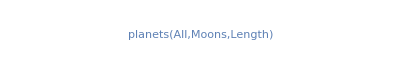

```mathematica
WordCloud[Normal[planets[All,"Moons",Length]]]
```

```mathematica
BarChart[ChartL]
```

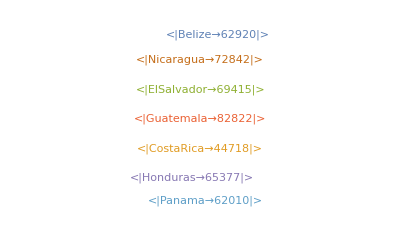

```mathematica
WordCloud[Association[#->StringLength[WikipediaData[#]]]&/@EntityList[EntityClass["Country","CentralAmerica"]]]
```

```mathematica
Association[#->StringLength[WikipediaData[#]]&/@EntityList[EntityClass["Country","CentralAmerica"]]]
```

<|Belize→62920,Costa Rica→44718,El Salvador→69415,Guatemala→82822,Honduras→65377,Nicaragua→72842,Panama→62010|>

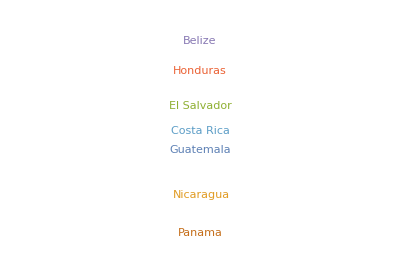

```mathematica
WordCloud[<|Entity["Country","Belize"]->62920,Entity["Country","CostaRica"]->44718,Entity["Country","ElSalvador"]->69415,Entity["Country","Guatemala"]->82822,Entity["Country","Honduras"]->65377,Entity["Country","Nicaragua"]->72842,Entity["Country","Panama"]->62010|>]
```

```mathematica
Take[{1,23,4},2]
```

{1,23}

```mathematica
fireballs=ResourceData["Fireballs and Bolides"]
```

ResourceObject::cloudc: You must connect to the Wolfram cloud to access the resource.

$Failed

```mathematica
GeoListPlot[{Entity["City",{"Bone","SulawesiSelatan","Indonesia"}],Entity["City",{"Kobojango","Bobonong","Botswana"}],Entity["City",{"Kurilsk","Sakhalin","Russia"}],Entity["City",{"Hihifo","Niuas","Tonga"}],Entity["City",{"Pingliang","Gansu","China"}],Entity["City",{"Illoqqortoormiut","Sermersooq","Greenland"}],Entity["City",{"Owenga","ChathamIslands","NewZealand"}],Entity["City",{"Grytviken","FalklandIslands","FalklandIslands"}],Entity["City",{"Sinjar","Nineveh","Iraq"}],Entity["City",{"Anadyr","Chukotka","Russia"}]},GeoLabels->Automatic]
```

-Graphics-

```mathematica
model=ExampleData[{"Geometry3D","StanfordBunny"}]
```

-Graphics3D-

```mathematica
Printout3D[model,"Sculpteo"]
```

Dataset[<>]

```mathematica
ColorNegate@Entity["MinorPlanet","Pluto"]["Image"]
```

-Graphics-

```mathematica
ImageAdd[-Graphics-,Darker[Red]]
```

-Graphics-